```mathematica
x1=0.5;h=0.052;n=24;
Array[xdata,n,0];Array[ydata,n,0];
ydata[0]=1.25066;ydata[1]=1.29388;ydata[2]=1.38282;ydata[3]=1.41156;
ydata[4]=1.49275;
ydata[5]=1.51117;
ydata[6]=1.58776;
ydata[7]=1.59938;
ydata[8]=1.6742;
ydata[9]=1.68197;
ydata[10]=1.75768;
ydata[11]=1.76405;
ydata[12]=1.84283;
ydata[13]=1.85019;
ydata[14]=1.93443;
ydata[15]=1.94466;
ydata[16]=2.03664;
ydata[17]=2.0516;
ydata[18]=2.15368;
ydata[19]=2.17516;
ydata[20]=2.28988;
ydata[21]=2.31975;
ydata[22]=2.44992;
ydata[23]=2.49015;
ydata[24]=2.63894;
ydata[25]=2.69173;
For[i=0,i<=n,i++,
xdata[i]=x1+h*i;];
MatrixForm[Table[{xdata[i],ydata[i]},{i,0,n}]]
```

(0.5 | 1.25066
0.552 | 1.29388
0.604 | 1.38282
0.656 | 1.41156
0.708 | 1.49275
0.76 | 1.51117
0.812 | 1.58776
0.864 | 1.59938
0.916 | 1.6742
0.968 | 1.68197
1.02 | 1.75768
1.072 | 1.76405
1.124 | 1.84283
1.176 | 1.85019
1.228 | 1.93443
1.28 | 1.94466
1.332 | 2.03664
1.384 | 2.0516
1.436 | 2.15368
1.488 | 2.17516
1.54 | 2.28988
1.592 | 2.31975
1.644 | 2.44992
1.696 | 2.49015
1.748 | 2.63894)

1.1353×10^13-2.77739×10^14 x+3.23356×10^15 x^2-2.3845×10^16 x^3+1.25048×10^17 x^4-4.96365×10^17 x^5+1.5497×10^18 x^6-3.9038×10^18 x^7+8.07544×10^18 x^8-1.38886×10^19 x^9+2.00306×10^19 x^10-2.43636×10^19 x^11+2.50738×10^19 x^12-2.18584×10^19 x^13+1.61258×10^19 x^14-1.00365×10^19 x^15+5.24091×10^18 x^16-2.27686×10^18 x^17+8.12966×10^17 x^18-2.34442×10^17 x^19+5.32393×10^16 x^20-9.16336×10^15 x^21+1.12329×10^15 x^22-8.73629×10^13 x^23+3.23945×10^12 x^24

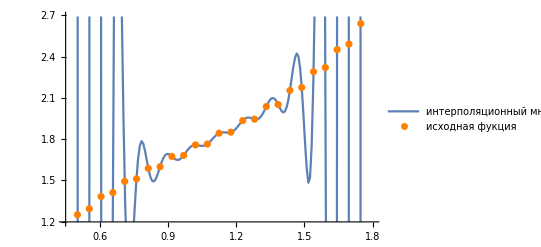

```mathematica
data25=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}];
inpln25:=InterpolatingPolynomial[data25,x];Collect[inpln25,x]
inplnPlot:=Plot[inpln25,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
Show[{inplnPlot25,pointsPlot}]
```

-184.493+2288.3 x-12753.5 x^2+42440.8 x^3-93876.7 x^4+145455. x^5-161953. x^6+130629. x^7-75791.5 x^8+30864.9 x^9-8378.24 x^10+1361.77 x^11-100.274 x^12

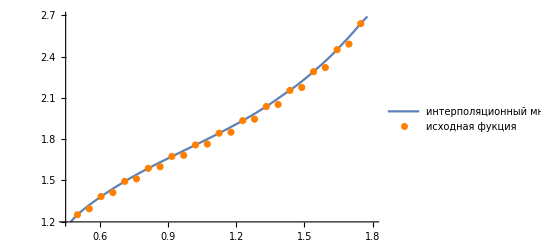

```mathematica
data12=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n,2}];
inpln12:=InterpolatingPolynomial[data12,x];Collect[inpln12,x]
inplnPlot12:=Plot[inpln12,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
Show[{inplnPlot12,pointsPlot}]
```

447.33-3756.73 x+13451.6 x^2-26799.6 x^3+32553.5 x^4-24724.3 x^5+11481.4 x^6-2984.23 x^7+332.781 x^8

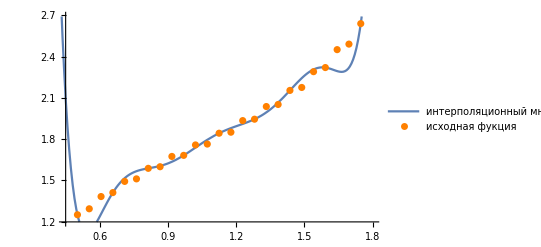

```mathematica
data8=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n,3}];
inpln8:=InterpolatingPolynomial[data8,x];Collect[inpln8,x]
inplnPlot8:=Plot[inpln8,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
Show[{inplnPlot8,pointsPlot}]
```

0.138994+3.32177 x-2.7172 x^2+1.0828 x^3-0.0843372 x^4

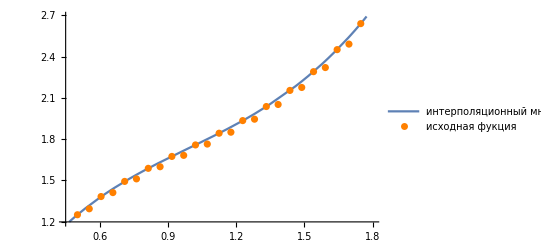

```mathematica
data5=Table[{N[xdata[i]],N[ydata[i]]},{i,0,n,6}];
inpln5:=InterpolatingPolynomial[data5,x];Collect[inpln5,x]
inplnPlot5:=Plot[inpln5,{x,0,n},PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}},PlotLegends->{"интерполяционный многочлен"}];
Show[{inplnPlot5,pointsPlot}]
```

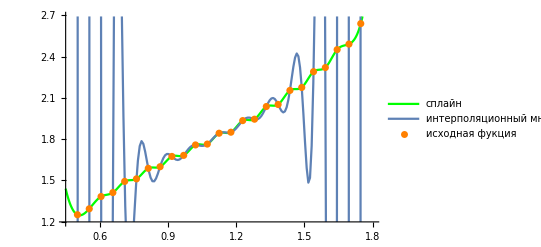

```mathematica
spln25:=Interpolation[data25,Method->"Spline"];
splnPlot25:=Plot[{spln25[x]},{x,xdata[0]-h,xdata[n]+h},PlotLegends->{"сплайн"},PlotStyle->Green,PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}}]
Show[{splnPlot25,inplnPlot25,pointsPlot}]
```

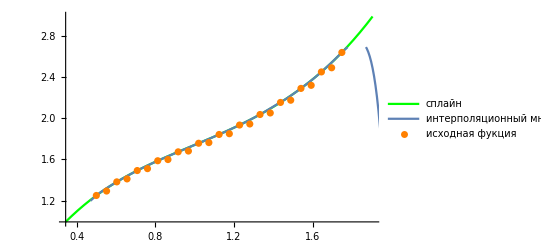

```mathematica
spln12:=Interpolation[data12,Method->"Spline"];
splnPlot12:=Plot[{spln12[x]},{x,xdata[0]-3*h,xdata[n]+3*h},PlotLegends->{"сплайн"},PlotStyle->Green]
Show[{splnPlot12,inplnPlot12,pointsPlot}]
```

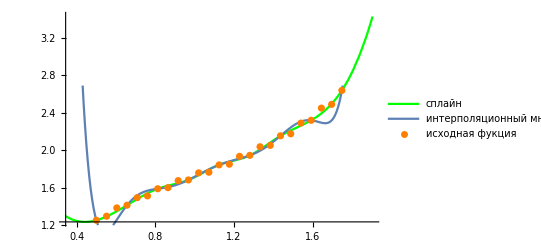

```mathematica
spln8:=Interpolation[data8,Method->"Spline"];
splnPlot8:=Plot[{spln8[x]},{x,xdata[0]-3*h,xdata[n]+3*h},PlotLegends->{"сплайн"},PlotStyle->Green]
Show[{splnPlot8,inplnPlot8,pointsPlot}]
```

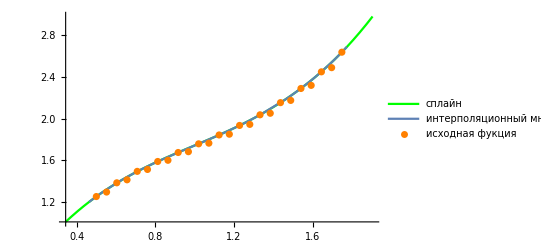

```mathematica
spln5:=Interpolation[data5,Method->"Spline"];
splnPlot5:=Plot[{spln5[x]},{x,xdata[0]-3*h,xdata[n]+3*h},PlotLegends->{"сплайн"},PlotStyle->Green]
Show[{splnPlot5,inplnPlot5,pointsPlot}]
```

0.73241+1.00624 x

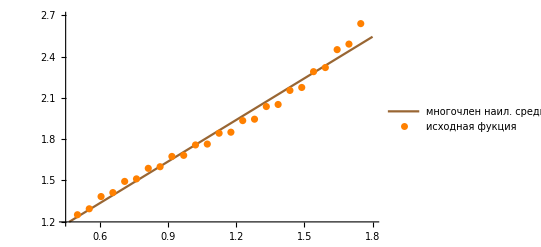

0.0601346

```mathematica
Clear[a,b]
rules1=FindFit[data25,a+b*x,{a,b},x];
y1=a+b*x/.rules1
f1[x_]:=a+b*x/.rules1;
quad1:=Plot[y1,{x,xdata[0]-h,xdata[n]+h},PlotStyle->Brown,PlotLegends->{"многочлен наил. среднекв. прибл."},
PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}}];
sko=0;
For[i=0,i<=n,i++,
sko=sko+(Abs[ydata[i]-f1[xdata[i]]])^2;]
Show[{quad1,pointsPlot}]
sko
```

1.04181+0.386758 x+0.275572 x^2

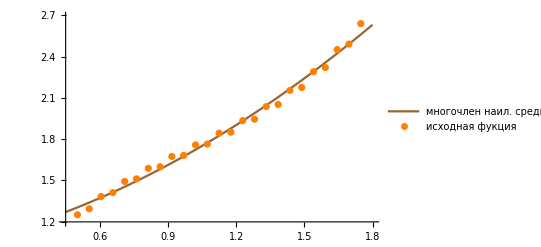

0.0302514

```mathematica
Clear[a,b]
rules1=FindFit[data25,a+b*x+c*x*x,{a,b,c},x];
y1=a+b*x+c*x*x/.rules1
f1[x_]:=a+b*x+c*x*x/.rules1;
quad1:=Plot[y1,{x,xdata[0]-h,xdata[n]+h},PlotStyle->Brown,PlotLegends->{"многочлен наил. среднекв. прибл."},
PlotRange->{{xdata[0]-h,xdata[n]+h},{ydata[0]-h,ydata[n]+h}}];
sko=0;
For[i=0,i<=n,i++,
sko=sko+(Abs[ydata[i]-f1[xdata[i]]])^2;]
Show[{quad1,pointsPlot}]
sko
```

```mathematica
∑_(i=0)^(n-1) ydata[i]*(xdata[i+1]-xdata[i])
∑_(i=1)^n ydata[i]*(xdata[i]-xdata[i-1])
∑_(i=0)^(n-1) (ydata[i]+ydata[i+1])/2(xdata[i+1]-xdata[i])
h/3*(ydata[0]+ydata[n]+4*∑_(i=1)^(n/2) ydata[2*i-1]+2*∑_(i=1)^(n/2-1) ydata[2*i])
```

2.28523

2.35742

2.32133

2.31346